## Исходные данные :

### Параметры :

Весовые коэффициенты:

```mathematica
ϵ1=1/N[#]&;
```

```mathematica
ϵ2=1/N[100*#]&;
```

Количество обучающих итераций, после которых происходит обновление классов:

```mathematica
λ=200;
```

Общее количество итераций (>= λ):

```mathematica
nOfi=600;
```

Возраст дуги, по истечении которого ее следует удалить:

```mathematica
ageMax=50;
```

Параметры, которые контролируют процесс удаления "шумовых" узлов:

```mathematica
c1=0.0001;
c2=1.0;
```

Максимально возможное количество связей для узла:

```mathematica
numberOfEdges=Infinity;
```

Инициализация количества классов:

```mathematica
classCount=0;
```

Счетчик классов и узлов:

```mathematica
classId=1;
nodeId=1;
```

### Создадим решетку:

```mathematica
LatticeData[]//TableForm//Framed
```

BaseCenteredMonoclinic
BaseCenteredOrthorhombic
BodyCenteredCubic
BodyCenteredOrthorhombic
CenteredTetragonal
CoxeterTodd
FaceCenteredCubic
FaceCenteredOrthorhombic
HexagonalClosePacking
HexagonalLattice
KorkineZolotarev
Leech
SimpleCubic
SimpleHexagonal
SimpleMonoclinic
SimpleOrthorhombic
SimpleTetragonal
SimpleTriclinic
SimpleTrigonal
SquareLattice
TetrahedralPacking

Размер решетки:

```mathematica
P=20;
```

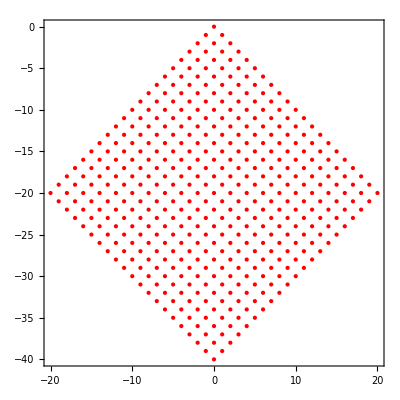

```mathematica
l=Normal@LatticeData["FaceCenteredCubic","Basis"];
latVec=Cases[l,{a_Integer,b_Integer,c_Integer}/;c==0->{a,b}];(*2D*)
lattice=Flatten[Table[i latVec[[1]]+j latVec[[2]],{i,0,P},{j,0,P}],1];
Graphics[{Red,PointSize[Large],Point@lattice},Frame->True,AspectRatio->1]
```

## Работа алгоритма ESOINN :

Набор промежуточных функций:

Вспомогательные функции:

```mathematica
findMinAndMax[firstWinner_,secondWinner_]:=Module[
{minId,maxId},
If[firstWinner⟦"nodeId"⟧≤secondWinner⟦"nodeId"⟧,

minId=firstWinner⟦"nodeId"⟧;
maxId=secondWinner⟦"nodeId"⟧;
{minId,maxId},

maxId=firstWinner⟦"nodeId"⟧;
minId=secondWinner⟦"nodeId"⟧;
{minId,maxId}
]
]
```

Добавление узла:

```mathematica
newNode[{x_,y_}]:=<|
"node id"->nodeId++,(*Warning! Uses global variable!*)
"coords"->{N@x,N@y},
"error"->0,
"number of wins"->0,
"possible number of edges"->numberOfEdges,
"density"->0,
"class id"->Null,
"points"->0
|>
```

Пороговое значение:

```mathematica
threshold[node_Association]:=Module[
{
coords=#⟦"coords"⟧&/@nodes,
nodeCoords=node⟦"coords"⟧,
tempCoords,
connectionsCoords=#⟦"coords"⟧&/@getConnectedNodes[node]
},
If[connectionsCoords=={},

tempCoords=PadRight[{nodeCoords},Length[coords],{nodeCoords}];
Min@MapThread[EuclideanDistance,{tempCoords,coords}],

tempCoords=PadRight[{nodeCoords},Length[connectionsCoords],{nodeCoords}];
Max@MapThread[EuclideanDistance,{tempCoords,connectionsCoords}]
]
]
```

Увеличиваем возраст соседей для узла:

```mathematica
addEdgesAge[firstWinner_Association]:=Module[
{positions,id=firstWinner⟦"node id"⟧,i,position},
positions=Position[edges,x_<->y_/;x_==id||y_==id]⟦All,1⟧;
If[positions≠{},

For[i=1,i≤Length[positions],i++,
position=positions⟦i⟧;
edges⟦position,2⟧+=1;
],

Null]
]
```

Средняя плотность:

```mathematica
meanDensity[classId_Integer,nodes_]:=If[classId==Null,0.0,
Module[
{density=0.0,selectedNodes},
selectedNodes=Select[nodes,#⟦"class id"⟧==classId&];
density=Total@(#⟦"density"⟧&/@selectedNodes);
density*=density/Length[selectedNodes]
]
]
```

Максимальная плотность:

```mathematica
maxDensity[classId_Integer,nodes_]:=Module[
{selectedNodes,max},
selectedNodes=Select[nodes,#⟦"class id"⟧==classId&];
max=Max@(#⟦"density"⟧&/@selectedNodes)
]
```

Граница для плотности:

```mathematica
densityThershold[mean_,max_]:=Which[
2.0*mean≥max,0.0,
(3.0*mean≥max)&&(max>2.0*mean),0.5,
_,1.0
]
```

Проверяем нужно ли объединить классы:

```mathematica
needMergeClasses[as1_Association,as2_Association]:=Module[
{classA=as1⟦"class id"⟧,classB=as2⟦"class id"⟧,meanA,maxA,meanB,maxB,thresholdA,thresholdB,minAB},
meanA=meanDensity[classA];
maxA=maxDensity[classA];
meanB=meanDensity[classA];
maxB=maxDensity[classA];
thresholdA=densityThershold[meanA,maxA];
thresholdB=densityThershold[meanB,maxB];
minAB=Min[as1⟦"density"⟧,as2⟦"density"⟧];
If[(minAB>thresholdA*maxA)&&(minAB>thresholdB*maxB),True,False]
]
```

Объединить классы:

```mathematica
mergeClasses[classId1_Integer,classId2_Integer]:=Module[
{minId=Min[classId1,classId2],i,nodeId},
For[i=1,i≤Length@nodes,i++,
nodeId=nodes⟦i⟧⟦"node id"⟧;
If[nodeId==classId1||nodeId==classId2,nodes⟦i⟧⟦"node id"⟧=minId];
]
]
```

Проверяем нужно ли ребро между узлами:

```mathematica
needAddEdge[firstWinner_Association,secondWinner_Association]:=Which[
(firstWinner["class id"]==Null) ||(secondWinner["class id"]==Null),True,
firstWinner["class id"]==secondWinner["class id"],True,
(firstWinner["class id"]≠secondWinner["class id"])&&(needMergeClasses[firstWinner,secondWinner]),True,
_,False
]
```

Добавляем ребро:

```mathematica
addEdge[firstWinner_,secondWinner_]:=Module[
{minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
AppendTo[edges,{minId<->maxId,0}];
]
```

Удаляем ребро :

```mathematica
removeEdge[firstWinner_,secondWinner_]:=Module[
{pos,minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
pos=Sequence@@Flatten@Position[edges⟦All,1⟧,minId<->maxId];
edges=Delete[edges,pos];
]
```

Удаляем "старые" ребра:

```mathematica
removeOldEdges:=Module[
{booleanList,Ages=edges⟦All,2⟧},
booleanList=#≤ageMax&/@Ages;
edges=Pick[edges,booleanList];
]
```

Проверяем наличие ребра между узлами:

```mathematica
edgeExistQ[firstWinner_,secondWinner_]:=Module[
{minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
 Select[edges(*global*),#⟦1⟧==minId<->maxId&]≠{}(*edges sorted as {min<->max,age}*)
]
```

Обнуляем "возраст" ребра:

```mathematica
makeAgeZero[firstWinner_,secondWinner_]:=
Module[
{pos,minId,maxId},
{minId,maxId}=findMinAndMax[firstWinner,secondWinner];
pos=Sequence@@Flatten@Position[edges⟦All,1⟧,minId<->maxId];
edges⟦pos,2⟧=0;
]
```

Среднее расстояние:

```mathematica
meanDistance[as_Association]:=Module[
{coordsOfConnections,asCoords=as⟦"coords"⟧,tempCoords},
coordsOfConnections=#⟦"coords"⟧&/@getConnectedNodes[as];
tempCoords=PadRight[{asCoords},Length[coordsOfConnections],{asCoords}];
Mean@MapThread[EuclideanDistance,{tempCoords,coordsOfConnections}]
]
```

Обновляем плотность:

```mathematica
updateDensity[as_Association]:=Module[
{mDistance=meanDistance[as]},
as⟦"number of wins"⟧+=1;
as⟦"points"⟧+=1./(1+mDistance)^2;
as⟦"density"⟧=as⟦"points"⟧/N[as⟦"number of wins"⟧]
]
```

Обновляем координаты:

```mathematica
updateCoords[firstWinner_Association,x_List]:=Module[
{coordsOfConnections,connectedNodes,numberOfWins=firstWinner⟦"number of wins"⟧,i},
firstWinner⟦"coords"⟧+=ϵ1[numberOfWins]*(x-firstWinner⟦"coords"⟧);
connectedNodes=getConnectedNodes[firstWinner];
coordsOfConnections=#⟦"coords"⟧&/@connectedNodes;
For[i=1,i≤Length[connectedNodes],i++,
connectedNodes⟦i⟧⟦"coords"⟧+=ϵ2[numberOfWins]*(x-connectedNodes⟦i⟧⟦"coords"⟧);
]
]
```

Получаем узлы, с которыми связан данный узел :

```mathematica
(*output is list of nodes (associtians)*)
getConnectedNodes[firstWinner_]:=Module[
{listOfIdsConnections,id=firstWinner⟦"node id"⟧,listOfIds,i,nodeId,listOfNodes={}},
listOfIdsConnections=Select[edges,#⟦1,1⟧==id||#⟦1,2⟧==id&]⟦All,1⟧;(*list of UndirectedEdge fuctions*)
listOfIds=listOfIdsConnections/.{x_<->y_/;x==id->y,x_<->y_/;y==id->x};(*list of Ids of nodes connected with firstWinner node*)
For[i=1,i≤Length[nodes],i++,
nodeId=nodes⟦i⟧⟦"node id"⟧;
If[Inner[Equal,PadRight[{nodeId},Length[listOfIds],nodeId],listOfIds,Or],AppendTo[listOfNodes,nodes⟦i⟧]]
];
listOfNodes
]
```

Ищем двух победителей:

```mathematica
findWinners[nodes_List,newSignal_List]:=Module[
{firstWinner,secondWinner,nearest1,nearest2},
nearest1=Flatten[Nearest[#⟦"coords"⟧&/@nodes,newSignal]];
firstWinner=Select[nodes,#⟦"coords"⟧==nearest1&]⟦1⟧;
nearest2=Flatten[Nearest[#⟦"coords"⟧&/@(Select[nodes,#⟦"coords"⟧≠nearest1&]),newSignal]];
secondWinner=Select[nodes,#⟦"coords"⟧==nearest2&]⟦1⟧;
{firstWinner,secondWinner}
]
```

Пометить смежные узлы меткой одного класса:

```mathematica
markAdjacentNodes[node_Association]:=Module[
{classId=classCount++,,listOfConnectedNodes=getConnectedNodes[node],listOfConnectedNodesWithoutMark,i,listOfIds},
node⟦"class id"⟧=classId;
listOfConnectedNodesWithoutMark=Select[listOfConnectedNodes,#⟦"class id"⟧==Null&];
For[i=1,i≤Length@listOfConnectedNodesWithoutMark,i++,
listOfConnectedNodesWithoutMark⟦i⟧⟦"class id"⟧=classId;
];
listOfIds=#⟦"node id"⟧&/@listOfConnectedNodesWithoutMark;
For[i=1,i≤nodes,i++,
If[Inner[Equal,PadRight[{nodes⟦i⟧⟦"node id"⟧},Length[listOfIds],nodes⟦i⟧⟦"node id"⟧],listOfIds,Or],
nodes=Delete[nodes,i];
];
nodes=nodes~Join~listOfConnectedNodesWithoutMark;
]
]
```

Разбивка класса на подклассы:

```mathematica
partitionClasses:=Module[
{i,edge,nodeId1,nodeId2,node1,node2},
For[i=1,i≤Length@edges,i++,
edge=edges⟦i,1⟧;
nodeId1=edge⟦1⟧;
nodeId2=edge⟦2⟧;
node1=Select[nodes,#⟦"node id"⟧==nodeId1&];
node2=Select[nodes,#⟦"node id"⟧==nodeId2&];
If[node1⟦"class id"⟧≠node2⟦"class id"⟧,

If[needMergeClasses[node1,node2],
mergeClasses[nodeId1,nodeId2],
removeEdge[node1,node2]
]
];
]
]
```

Удаляем "шумовые" узлы:

```mathematica
deleteNoiseNode:=Module[
{i,listOfConnectedNodes,numberOfConnectedNodes,mean,node},
For[i=1,i≤Length@nodes,i++,
node=nodes⟦i⟧;
listOfConnectedNodes=getConnectedNodes[node];
numberOfConnectedNodes=Length[listOfConnectedNodes];
mean=meanDensity[node⟦"class id"⟧];
If[(numberOfConnectedNodes==2&&node⟦"density"⟧<c1*mean)||
(numberOfConnectedNodes==1&&node⟦"density"⟧<c2*mean)||
(numberOfConnectedNodes==0),

nodes=Delete[nodes,i];
deleteEdgesConnectedWithNode;
deleteEdgesConnectedWithNode[node];
]
]
]
```

Удалить все ребра, связанные с данным узлом :

```mathematica
deleteEdgesConnectedWithNode[node_Association]:=Module[
{listOfConnectedIds=#⟦"node id"⟧&/@getConnectedNodes[node],i,edge},
For[i=1,i≤Length@edges,i++,
edge=edges⟦i,1⟧;
If[MemberQ[listOfConnectedIds,edge⟦1⟧]||MemberQ[listOfConnectedIds,edge⟦2⟧],edges=Delete[edges,i]];
]
]
```

Инициализация:

```mathematica
Clear[nodes];
node1=newNode[RandomChoice[lattice]];
node2=newNode[RandomChoice[lattice]];
nodes={node1,node2};(*make esoinn graph*)
edges={};
```

Основной цикл работы:

```mathematica
For[i=1,i≤nOfi,i++,
If[Mod[i,λ]≠0,

newSignal=RandomChoice[lattice];(*newSignal is a List*)

{firstWinner,secondWinner}=findWinners[nodes,newSignal];(*output is associations*)

dist1=EuclideanDistance[firstWinner⟦"coords"⟧,newSignal];
dist2=EuclideanDistance[secondWinner⟦"coords"⟧,newSignal];

If[(dist1>threshold[firstWinner])||(dist2>threshold[secondWinner]),

node=newNode[newSignal];
AppendTo[nodes,node];
Continue[];
];

(*addEdgesAge[firstWinner];

If[needAddEdge[firstWinner,secondWinner],

If[edgeExistQ[firstWinner,secondWinner],
makeAgeZero[firstWinner,secondWinner],
addEdge[firstWinner,secondWinner]
],
If[edgeExistQ[firstWinner,secondWinner],removeEdge[firstWinner,secondWinner]];
];

updateDensity[firstWinner];

updateCoords[firstWinner,newSignal];

removeOldEdges,(*dangerous function*)

(*If the number of input signals generated so far is an integer multiple of parameter λ do:*)
nodes=SortBy[nodes,#⟦"density"⟧&];(*Sort by density parameter*)
Module[
{i,node},
For[i=1,i≤Length[nodes],i++,
If[nodes⟦i⟧⟦"node id"⟧==Null,

nodes⟦i⟧⟦"node id"⟧=classCount;
markAdjacentNodes[nodes⟦i⟧];
];
]
];

partitionClasses;

deleteNoiseNode;
*)
]
]
```

Set::shape: Lists {firstWinner, secondWinner} and {<| "node id" → 7, "coords" → {-6., -20.}, "error" → 0, "number of wins" → 0, "possible number of edges" → ∞, "density" → 0, "class id" → Null, "points" → 0 |>} are not the same shape.

Set::shape: Lists {firstWinner, secondWinner} and {} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.